maxR=30

3.64958×10^-9

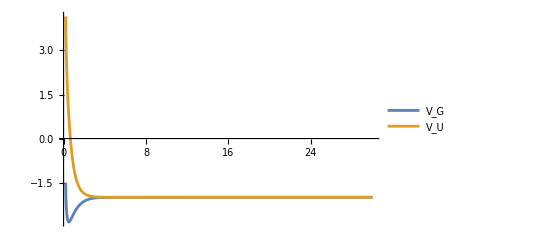

```mathematica
(* Radiative Quenching, Chapter 3 *)
(* This one uses my paper *)

(*electron mass *)
Subscript[m, e]=1;
(* Proton Mass *)
Subscript[m, p]=1836;
(* Reduced Mass *)
μ=Subscript[m, p]/2;
hbar= 1;  
hbarSI =1.054571817*^-34;
cLight=137.036 ;(*SpeedOfLight, atomic units*)
cLightSI= 299792458 ;(*SpeedOfLight, m/s*)
oneSec = 2.418884326509*^-17;  (* 1 sec SI <-> 1 sec AU *)
aBorh = 5.29177*^-11;   (* Si <-> AU *)
eps0=1/(4π);
eps0SI=8.854187817*^-12;

(* RawData format R,E, E + 1/R,A,p *)

vSg1RawData = Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/gerade1sV2.mx"];
vSu2RawData = Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/ungerade1sV2.mx"];

vSg1Data =vSg1RawData[[1;;44]];
vSu2Data = vSu2RawData[[1;;44]];

(* Calculate the Transition Dipole Moment *)
(* Upper Limit for integration *)
maxR = vSg1Data[[Length[vSg1Data]]][[1]];
Print["maxR=",maxR]

(* Load Potential curves for 1sg, 2sg states 
"R","p", "A","E","E+1/r"*)
(* 1sg state, potential curve *)
vG=Interpolation[Transpose[{vSg1Data[[All,1]],vSg1Data[[All,3]]}], InterpolationOrder->3];
(* 2sg state, potential curve *)
vU=Interpolation[Transpose[{vSu2Data[[All,1]],vSu2Data[[All,3]]}], InterpolationOrder->3];

deltaV[r_]:=Abs[vG[r]-vU[r]];
deltaV[20]
Plot[{vG[r],vU[r]},{r,0.2,maxR}, PlotRange->Full, PlotLegends->{"V_G","V_U"}]
```

```mathematica
Print[vSg1Data[[19]][[1]],", ",vSg1Data[[19]][[4]],", ",vSg1Data[[19]][[5]],", ",vSu2Data[[19]][[4]],", ",vSu2Data[[19]][[5]]]
Print[vSg1Data[[20]][[1]],", ",vSg1Data[[20]][[4]],", ",vSg1Data[[20]][[5]],", ",vSu2Data[[20]][[4]],", ",vSu2Data[[20]][[5]]]
```

5., 3437.09, 5.24591, 17397.4, 5.2446

6, 127499., 6.24594, 54879.4, 6.2457

```mathematica
(* Compute the Dipole momement D(r) for the single value of R *)
singleDR[R_,a1_,p1_,a2_,p2_, maxR_]:=Module[{lSol1,mSol1, lSol2,mSol2,norm1, norm2,dInt, lm1, lm2},
(* 1s wavefunction *)
(* x = λ, y = μ **)
l1=NDSolveValue[{(ξ^2-1)L''[ξ]+ξ * L'[ξ]+ (a1 +2 R ξ -p1^2 ξ^2)L[ξ]==0 ,L[1.01]==0,L'[1.001]==1 },L,{ξ,1.001,maxR}];
m1=NDSolveValue[{(1-η^2)M''[η]-η *M'[η] - (a1 - p1^2 η^2)M[η]==0, M'[0]==0,M'[0.999]==1}, M,{η,-.999,.999}];
(* 2s wavefunction *) 
l2=NDSolveValue[{(ξ^2-1)L''[ξ]+ξ * L'[ξ]+ (a2+2 R ξ -p2^2 ξ^2)L[ξ]==0 ,L[1.01]==0,L'[1.001]==1 },L,{ξ,1.01,maxR}];
m2=NDSolveValue[{(1-η^2)M''[η]-yη *M'[η] - (a2 - p2^2 η^2)M[η]==0, M'[0]==0,M'[0.999]==1}, M,{η,0,.999}];

Print["R=",R];
(* Compute <ψ|ψ> = <Subscript[ψ, 1s]|Subscript[ψ, 1s]> + <Subscript[ψ, 2s]|Subscript[ψ, 2s]> *)
(* <Subscript[ψ, 1s]|Subscript[ψ, 1s]> *)
norm1=Sqrt[NIntegrate[Abs[l1[ξ] m1[η]]^2,{η,-.999,.999},{ξ,1.001,maxR}]];
(* <Subscript[ψ, 2s]|Subscript[ψ, 2s]> *)
norm2=Sqrt[NIntegrate[Abs[l2[ξ]m2[η]]^2,{η,-.999,.999},{ξ,1.001,maxR}]];

lmNorm1[ξ_,η_]:=1/norm1 l1[ξ]m1[η];
lmNorm2[ξ_,η_]:=1/norm2 l2[ξ]m2[η];

dInt=(R/2)^3 NIntegrate[Conjugate[lmNorm1[ξ,η]]ξ η lmNorm2[ξ,η]((ξ^2-η^2)/(√(ξ^2-1)√(1-η^2))),{η,-0.999,0.999},{ξ,1.001,maxR}];
{R,dInt }
];


(*singleDR[vSg1Data[[19]][[1]],vSg1Data[[19]][[4]],vSg1Data[[19]][[5]],vSu2Data[[19]][[4]],vSu2Data[[19]][[5]],30]
singleDR[vSg1Data[[20]][[1]],vSg1Data[[20]][[4]],vSg1Data[[20]][[5]],vSu2Data[[20]][[4]],vSu2Data[[20]][[5]],30]*)
```

```mathematica
(* Get all Rs, and coefficients A and p and calculate D(R) for all Rs *)
(* RawData format R,E, E + 1/R,A,p *)
inputData = Transpose[{vSg1Data[[All,1]],vSg1Data[[All,4]],vSg1Data[[All,5]],vSu2Data[[All,4]],vSu2Data[[All,5]]}];

allDR =Map[singleDR[#[[1]],#[[2]],#[[3]],#[[4]],#[[5]], maxR] &, inputData];
allDR
```

NDSolveValue::ndnum: Encountered non-numerical value for a derivative at η == -0.999.

R=0.1

NDSolveValue::ndnum: Encountered non-numerical value for a derivative at η == -0.999.

NDSolveValue::dsvar: -η cannot be used as a variable.

NIntegrate::inumr: The integrand Abs[«1» NDSolveValue[{Times[«3»]+Times[«3»]+Times[«2»]==0,M[-0.999]==1,M'[0.999]==0},M,{η,-0.999,0.999}][η]]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-999/1000,999/1000},{1001/1000,1.01}}.

NDSolveValue::ndnum: Encountered non-numerical value for a derivative at η == -0.999.

General::stop: Further output of NDSolveValue::ndnum will be suppressed during this calculation.

NDSolveValue::dsvar: -η cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

NIntegrate::inumr: The integrand Abs[«1» NDSolveValue[{Times[«3»]+Times[«3»]+Times[«2»]==0,M[-0.999]==1,M'[0.999]==0},M,{η,-0.999,0.999}][η]]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-999/1000,999/1000},{1001/1000,1.01}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::write: Tag Times in -η is Protected.

General::stop: Further output of NIntegrate::write will be suppressed during this calculation.

```mathematica
(* Dipole moment in SI units *)
drAUtoSI = 8.478*^-30; (* Cm *)
allDRSI=allDR;
allDRSI[[All,2]] =allDR[[All,2]]*drAUtoSI;
allDRSI

dR =Interpolation[Transpose[{allDR[[All,1]],allDR[[All,2]]}], InterpolationOrder->3];
Plot[dR[r],{r,0.1, maxR}, PlotLabel->"D(R)", AxesLabel->{"R(a_0)", "D(R)(in a.u.)"}, PlotRange->Full]

dRSI =Interpolation[Transpose[{allDRSI[[All,1]],allDRSI[[All,2]]}], InterpolationOrder->3];
Plot[dRSI[r],{r,0.1, maxR}, PlotLabel->"D(R)", AxesLabel->{"R(a_0)", "D(R) (units of C m)"}, PlotRange->Full]
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand 3.411867723334565×10^-744 x «4» InterpolatingFunction[{{-0.999,0.999}},{5,3,2,{11586},{4},0,0,0,0,Automatic,{},{},False},{{-0.999,-0.999,«47»,-0.998717,«11536»}},{{1.,0.,1.7009×10^8},{1.,0.000145167,1.7009×10^8},{1.,0.000290334,1.7009×10^8},«45»,{13.4415,155247.,1.74188×10^9},{15.8771,182486.,2.03469×10^9},«11536»},{Automatic}][y] «1» has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{-0.9,0.9},{1.001,30}}.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand 3.411867723334565×10^-744 x «4» InterpolatingFunction[{{-0.999,0.999}},{5,3,2,{11586},{4},0,0,0,0,Automatic,{},{},False},{{-0.999,-0.999,«47»,-0.998717,«11536»}},{{1.,0.,1.7009×10^8},{1.,0.000145167,1.7009×10^8},{1.,0.000290334,1.7009×10^8},«45»,{13.4415,155247.,1.74188×10^9},{15.8771,182486.,2.03469×10^9},«11536»},{Automatic}][y] «1» has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{-0.9,0.9},{1.001,30}}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand 3.411867723334565×10^-744 x «4» InterpolatingFunction[{{-0.999,0.999}},{5,3,2,{11586},{4},0,0,0,0,Automatic,{},{},False},{{-0.999,-0.999,«47»,-0.998717,«11536»}},{{1.,0.,1.7009×10^8},{1.,0.000145167,1.7009×10^8},{1.,0.000290334,1.7009×10^8},«45»,{13.4415,155247.,1.74188×10^9},{15.8771,182486.,2.03469×10^9},«11536»},{Automatic}][y] «1» has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{-0.9,0.9},{1.001,30}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand 3.411867723334565×10^-744 x «4» InterpolatingFunction[{{-0.999,0.999}},{5,3,2,{11586},{4},0,0,0,0,Automatic,{},{},False},{{-0.999,-0.999,«47»,-0.998717,«11536»}},{{1.,0.,1.7009×10^8},{1.,0.000145167,1.7009×10^8},{1.,0.000290334,1.7009×10^8},«45»,{13.4415,155247.,1.74188×10^9},{15.8771,182486.,2.03469×10^9},«11536»},{Automatic}][y] «1» has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{-0.9,0.9},{1.001,30}}.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand 3.411867723334565×10^-744 x «4» InterpolatingFunction[{{-0.999,0.999}},{5,3,2,{11586},{4},0,0,0,0,Automatic,{},{},False},{{-0.999,-0.999,«47»,-0.998717,«11536»}},{{1.,0.,1.7009×10^8},{1.,0.000145167,1.7009×10^8},{1.,0.000290334,1.7009×10^8},«45»,{13.4415,155247.,1.74188×10^9},{15.8771,182486.,2.03469×10^9},«11536»},{Automatic}][y] «1» has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{-0.9,0.9},{1.001,30}}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand 3.411867723334565×10^-744 x «4» InterpolatingFunction[{{-0.999,0.999}},{5,3,2,{11586},{4},0,0,0,0,Automatic,{},{},False},{{-0.999,-0.999,«47»,-0.998717,«11536»}},{{1.,0.,1.7009×10^8},{1.,0.000145167,1.7009×10^8},{1.,0.000290334,1.7009×10^8},«45»,{13.4415,155247.,1.74188×10^9},{15.8771,182486.,2.03469×10^9},«11536»},{Automatic}][y] «1» has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{-0.9,0.9},{1.001,30}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand 3.411867723334565×10^-744 x «4» InterpolatingFunction[{{-0.999,0.999}},{5,3,2,{11586},{4},0,0,0,0,Automatic,{},{},False},{{-0.999,-0.999,«47»,-0.998717,«11536»}},{{1.,0.,1.7009×10^8},{1.,0.000145167,1.7009×10^8},{1.,0.000290334,1.7009×10^8},«45»,{13.4415,155247.,1.74188×10^9},{15.8771,182486.,2.03469×10^9},«11536»},{Automatic}][y] «1» has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{-0.9,0.9},{1.001,30}}.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand 3.411867723334565×10^-744 x «4» InterpolatingFunction[{{-0.999,0.999}},{5,3,2,{11586},{4},0,0,0,0,Automatic,{},{},False},{{-0.999,-0.999,«47»,-0.998717,«11536»}},{{1.,0.,1.7009×10^8},{1.,0.000145167,1.7009×10^8},{1.,0.000290334,1.7009×10^8},«45»,{13.4415,155247.,1.74188×10^9},{15.8771,182486.,2.03469×10^9},«11536»},{Automatic}][y] «1» has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{-0.9,0.9},{1.001,30}}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand 3.411867723334565×10^-744 x «4» InterpolatingFunction[{{-0.999,0.999}},{5,3,2,{11586},{4},0,0,0,0,Automatic,{},{},False},{{-0.999,-0.999,«47»,-0.998717,«11536»}},{{1.,0.,1.7009×10^8},{1.,0.000145167,1.7009×10^8},{1.,0.000290334,1.7009×10^8},«45»,{13.4415,155247.,1.74188×10^9},{15.8771,182486.,2.03469×10^9},«11536»},{Automatic}][y] «1» has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{-0.9,0.9},{1.001,30}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

{{0.1,4.42877×10^-19},{0.2,-1.02936×10^-20},{0.3,2.59276×10^-11},{0.4,1.94719×10^-10},{0.5,-1.6729×10^-32},{0.6,8.06136×10^-10},{0.7,1.33149×10^-9},{0.8,-8.34067×10^-52},{0.9,1.73022×10^-9},{1.,-2.12577×10^-8},{1.1,2.25406×10^-9},{1.5,8.79195×10^-27},{2.,-7.93122×10^-6},{2.5,5.00303×10^-26},{3.,1.15694×10^-78},{3.5,-2.38294×10^-25},{4.,-2.10793×10^-25},{4.5,-5.37934×10^-80},{5.,-2.79103×10^-24},{6,2.28906×10^-28 NIntegrate[Conjugate[lmNorm1[x,y]] x y lmNorm2[x,y] (x^2-y^2),{y,-0.9,0.9},{x,1.001,30}]},{7,3.63494×10^-28 NIntegrate[Conjugate[lmNorm1[x,y]] x y lmNorm2[x,y] (x^2-y^2),{y,-0.9,0.9},{x,1.001,30}]},{8,0.},{9,7.72558×10^-28 NIntegrate[Conjugate[lmNorm1[x,y]] x y lmNorm2[x,y] (x^2-y^2),{y,-0.9,0.9},{x,1.001,30}]},{10,1.05975×10^-27 NIntegrate[Conjugate[lmNorm1[x,y]] x y lmNorm2[x,y] (x^2-y^2),{y,-0.9,0.9},{x,1.001,30}]},{11,1.41053×10^-27 NIntegrate[Conjugate[lmNorm1[x,y]] x y lmNorm2[x,y] (x^2-y^2),{y,-0.9,0.9},{x,1.001,30}]},{12,1.83125×10^-27 NIntegrate[Conjugate[lmNorm1[x,y]] x y lmNorm2[x,y] (x^2-y^2),{y,-0.9,0.9},{x,1.001,30}]},{13,2.32827×10^-27 NIntegrate[Conjugate[lmNorm1[x,y]] x y lmNorm2[x,y] (x^2-y^2),{y,-0.9,0.9},{x,1.001,30}]},{14,2.90795×10^-27 NIntegrate[Conjugate[lmNorm1[x,y]] x y lmNorm2[x,y] (x^2-y^2),{y,-0.9,0.9},{x,1.001,30}]},{15,3.57666×10^-27 NIntegrate[Conjugate[lmNorm1[x,y]] x y lmNorm2[x,y] (x^2-y^2),{y,-0.9,0.9},{x,1.001,30}]},{16,4.34074×10^-27 NIntegrate[Conjugate[lmNorm1[x,y]] x y lmNorm2[x,y] (x^2-y^2),{y,-0.9,0.9},{x,1.001,30}]},{17,5.20655×10^-27 NIntegrate[Conjugate[lmNorm1[x,y]] x y lmNorm2[x,y] (x^2-y^2),{y,-0.9,0.9},{x,1.001,30}]},{18,6.18046×10^-27 NIntegrate[Conjugate[lmNorm1[x,y]] x y lmNorm2[x,y] (x^2-y^2),{y,-0.9,0.9},{x,1.001,30}]},{19,0.},{20,8.478×10^-27 NIntegrate[Conjugate[lmNorm1[x,y]] x y lmNorm2[x,y] (x^2-y^2),{y,-0.9,0.9},{x,1.001,30}]},{21,9.81434×10^-27 NIntegrate[Conjugate[lmNorm1[x,y]] x y lmNorm2[x,y] (x^2-y^2),{y,-0.9,0.9},{x,1.001,30}]},{22,1.12842×10^-26 NIntegrate[Conjugate[lmNorm1[x,y]] x y lmNorm2[x,y] (x^2-y^2),{y,-0.9,0.9},{x,1.001,30}]},{23,1.2894×10^-26 NIntegrate[Conjugate[lmNorm1[x,y]] x y lmNorm2[x,y] (x^2-y^2),{y,-0.9,0.9},{x,1.001,30}]},{24,1.465×10^-26 NIntegrate[Conjugate[lmNorm1[x,y]] x y lmNorm2[x,y] (x^2-y^2),{y,-0.9,0.9},{x,1.001,30}]},{25,1.65586×10^-26 NIntegrate[Conjugate[lmNorm1[x,y]] x y lmNorm2[x,y] (x^2-y^2),{y,-0.9,0.9},{x,1.001,30}]},{26,1.86262×10^-26 NIntegrate[Conjugate[lmNorm1[x,y]] x y lmNorm2[x,y] (x^2-y^2),{y,-0.9,0.9},{x,1.001,30}]},{27,2.08591×10^-26 NIntegrate[Conjugate[lmNorm1[x,y]] x y lmNorm2[x,y] (x^2-y^2),{y,-0.9,0.9},{x,1.001,30}]},{28,2.32636×10^-26 NIntegrate[Conjugate[lmNorm1[x,y]] x y lmNorm2[x,y] (x^2-y^2),{y,-0.9,0.9},{x,1.001,30}]},{29,2.58462×10^-26 NIntegrate[Conjugate[lmNorm1[x,y]] x y lmNorm2[x,y] (x^2-y^2),{y,-0.9,0.9},{x,1.001,30}]},{30,2.86133×10^-26 NIntegrate[Conjugate[lmNorm1[x,y]] x y lmNorm2[x,y] (x^2-y^2),{y,-0.9,0.9},{x,1.001,30}]}}

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand 3.411867723334565×10^-744 x «4» InterpolatingFunction[{{-0.999,0.999}},{5,3,2,{11586},{4},0,0,0,0,Automatic,{},{},False},{{-0.999,-0.999,«47»,-0.998717,«11536»}},{{1.,0.,1.7009×10^8},{1.,0.000145167,1.7009×10^8},{1.,0.000290334,1.7009×10^8},«45»,{13.4415,155247.,1.74188×10^9},{15.8771,182486.,2.03469×10^9},«11536»},{Automatic}][y] «1» has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{-0.9,0.9},{1.001,30}}.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand 3.411867723334565×10^-744 x «4» InterpolatingFunction[{{-0.999,0.999}},{5,3,2,{11586},{4},0,0,0,0,Automatic,{},{},False},{{-0.999,-0.999,«47»,-0.998717,«11536»}},{{1.,0.,1.7009×10^8},{1.,0.000145167,1.7009×10^8},{1.,0.000290334,1.7009×10^8},«45»,{13.4415,155247.,1.74188×10^9},{15.8771,182486.,2.03469×10^9},«11536»},{Automatic}][y] «1» has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{-0.9,0.9},{1.001,30}}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand 3.411867723334565×10^-744 x «4» InterpolatingFunction[{{-0.999,0.999}},{5,3,2,{11586},{4},0,0,0,0,Automatic,{},{},False},{{-0.999,-0.999,«47»,-0.998717,«11536»}},{{1.,0.,1.7009×10^8},{1.,0.000145167,1.7009×10^8},{1.,0.000290334,1.7009×10^8},«45»,{13.4415,155247.,1.74188×10^9},{15.8771,182486.,2.03469×10^9},«11536»},{Automatic}][y] «1» has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{-0.9,0.9},{1.001,30}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand 3.411867723334565×10^-744 x «4» InterpolatingFunction[{{-0.999,0.999}},{5,3,2,{11586},{4},0,0,0,0,Automatic,{},{},False},{{-0.999,-0.999,«47»,-0.998717,«11536»}},{{1.,0.,1.7009×10^8},{1.,0.000145167,1.7009×10^8},{1.,0.000290334,1.7009×10^8},«45»,{13.4415,155247.,1.74188×10^9},{15.8771,182486.,2.03469×10^9},«11536»},{Automatic}][y] «1» has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{-0.9,0.9},{1.001,30.}}.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumri: The integrand 3.411867723334565×10^-744 x «4» InterpolatingFunction[{{-0.999,0.999}},{5,3,2,{11586},{4},0,0,0,0,Automatic,{},{},False},{{-0.999,-0.999,«47»,-0.998717,«11536»}},{{1.,0.,1.7009×10^8},{1.,0.000145167,1.7009×10^8},{1.,0.000290334,1.7009×10^8},«45»,{13.4415,155247.,1.74188×10^9},{15.8771,182486.,2.03469×10^9},«11536»},{Automatic}][y] «1» has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{-0.9,0.9},{1.001,30.}}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand 3.411867723334565×10^-744 x «4» InterpolatingFunction[{{-0.999,0.999}},{5,3,2,{11586},{4},0,0,0,0,Automatic,{},{},False},{{-0.999,-0.999,«47»,-0.998717,«11536»}},{{1.,0.,1.7009×10^8},{1.,0.000145167,1.7009×10^8},{1.,0.000290334,1.7009×10^8},«45»,{13.4415,155247.,1.74188×10^9},{15.8771,182486.,2.03469×10^9},«11536»},{Automatic}][y] «1» has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{-0.9,0.9},{1.001,30.}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

```mathematica
aR[R_]:=π/(hbar eps0)(dR[R])^2((vU[R]-vG[R])/cLight)^2;


aRSI[R_]:=π/(hbarSI eps0SI)(dRSI[R])^2(((vU[R]-vG[R])4.35974*^-18)/cLight)^2;


Plot[aR[r],{r,.1,  10}, PlotLabel->"A(R)", AxesLabel->{"R(a_0)", "A(R)"}, PlotRange->Full]
Plot[aRSI[r],{r,.1,  10}, PlotLabel->"A(R)", AxesLabel->{"R(a_0)", "A(R) (s^-1)"}, PlotRange->Full]
```

-Graphics-

-Graphics-